# Graphics Primitives and Directives

In this lesson, we learn about using graphics primitives and directives in Mathematica. With graphics primitives, Mathematica can efficiently store and render (draw) 2D and 3D objects or combinations of objects. Directives will allow us to control the way that objects are rendered. We will focus mostly on points and lines in this lesson, although there are many more types of primitives.

Conveniently, points and lines have heads of Point and Line, respectively. For example,

```mathematica
Point[{1,2}]
```

represents a point with coordinates (1, 2), and

```mathematica
Line[{{1, 2}, {2,3}, {3, 10}}]
```

represents line segments connecting the points (1,2) to (2, 3) and connecting (2,3) to (3,10). The syntax for points and lines in three dimensions is similar. The function Graphics will output a two-dimensional graphical image from an input of a list of primitives (in three dimensions, the command is called Graphics3D).

```mathematica
Graphics[{Point[{1,2}]}] (* Notice that Graphics needs a list as input *)
```

-Graphics-

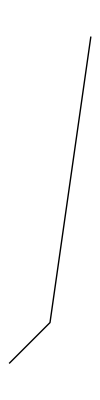

```mathematica
Graphics[{Line[{{1, 2}, {2,3}, {3, 10}}]}] (* notice that Line needs a list containing the points and that Graphics needs a list as input *)
```

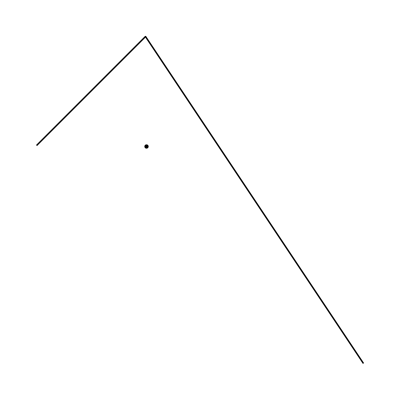

```mathematica
(* we can combine primitives in a list as input for Graphics *)
Graphics[{Line[{{1,4}, {2, 5}, {4, 2}}], Point[{2, 4}]}]
```

The Wolfram Language allows you detailed control over the way that graphics objects are rendered. The combination of sequentially-acting graphics directives (options that change the way that objects are drawn), together with hierarchical style specifications, makes possible succinct descriptions of complex graphical scenes. To use a directive, create a list with the directives first, primitive last, and evaluate Graphics at the list. The following example shows how the addition of a few directions can radically change the way that a primitive is rendered.

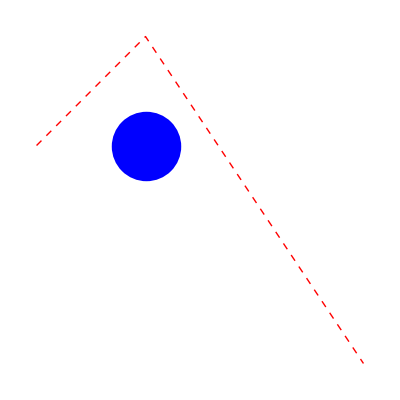

```mathematica
Graphics[{{Dashed, Red, Line[{{1,4}, {2, 5}, {4, 2}}]}, {Blue, PointSize[.2],Point[{2, 4}]}}]
```

Exercise 1: 
	1. Render 15 random points (x, y) in two dimensions where x and y are integers with 0 ≤ x, y ≤ 100.
	2. Render 15 random points (x, y, z) in three dimensions where x, y, z are integers with 0 ≤ x, y, z ≤ 100 and where each point is rendered with random size (within reason!). See the graphics directive PointSize.

Exercise 2: Another type of graphics primitive is Disk and another directive is Hue. Use the follow code to understand how the directive Hue[k] will affect the rendering of graphics and answer the following questions.

```mathematica
Manipulate[Graphics[{Hue[k], Disk[]}], {k, 0, 1, .01}]
```

1. What value of k corresponds to drawing the primitive in yellow?

	2. What value of k corresponds to drawing the primitive in blue?
	
	3. What value of k corresponds to drawing the primitive in red?

Exercise 3: 
	1. Render a set of line segments that connects 10 random points (x, y) in two dimensions where x, y are integers with 0 ≤ x, y ≤ 100.
	
	2. Repeat part (1), but render it so that each segment is of a random color.
	
	3. Repeat part (1), but render it so that each segment slowly transitions from blue to red. (This can be done with Hue, but you can also check out the function Blend.)

Exercise 4: Consider the polygon P defined by the line segments below.

```mathematica
P = Line[{0,0},{1, 1}, {2, 5}, {3, 3}, {4,5},{5,1}, {0,0}]
```

1. Render the polygon P. Fix the view so that the portion of the plane visible is -10 ≤ x, y, ≤ 60. See the graphics option PlotRange for this.

	2. We will create new polygons by taking each vertex (x, y) of P and replacing with (f(x), f(y)) using Map.
		a. With the same plot range, render the polygon for f(x) =arctan x. 
		
		b. Using manipulate for the parameter -6 ≤ k ≤ 6, render the polygon for f(x) = x^2 - k x.
		
		c. For what value of k does the polygon in part (b) become the union of two triangles?

Exercise 5: Imagine a point mass at the origin of mass m_1 and other point mass located at (10,0) of mass m_2 connected by a weightless horizontal rod. Using manipulate to allow you to change m_1, m_2, render these points (sized proportionally to their respective mass) and the rod along with a vertical arrow pointing at the center of mass of these points. For the arrow, check out the graphics primitive Arrow. Make it look nice by adding color and other features. For those that have forgotten how to find center of mass of an n point system, check this page.

Exercise 6:  Suppose that we write a real number x in base 4. This can be easily done in Mathematica (in any base) using the function RealDigits. We will translate the digits of x in base 4 into a sequence of line segments in the following way:
	Begin at the point (0,0).
	If the first digit is a 0, connect this point to (1,0) (that is, move right).
	If the first digit is a 1, connect this point to (0,1) (that is, move up). 
	If the first digit is a 2 or 3, move left or down respectively.
	Repeat this process for each subsequent digit.
	
Here is what the line segments look like for the first 10000 digits of √2, rendered so that the hue varies smoothly from start to finish.

(The function Accumulate might come in handy.)

		1. Render the line segments for the first 10000 digits of the rational number 1/3.
	
		2. Render the line segments for the first 10000 digits of the rational number 1127/1543.
	
		3. Render the line segments for the digits of the integer
		114235507611037187537074750347199975418
		
		4. Render the line segments for the first 10000 digits of the irrational number π.
		
		5. Render the line segments for the first 10000 digits of the irrational number ⅇ.
		
		6. Render the line segment for a 10000-digit integer chosen uniformly at random in base 4. Which renderings above look most like this one? (This idea has been introduced in the study of the structure of π in base 10. It is suspected that π is a normal number, meaning that in the limit, every string of length n in π  occurs approximately 1/10^n of the time. You can find more information about normal numbers at this wikipedia page. 
		
		7. Comment on the difference in structure of these line segments when x is rational vs irrational. How does this related to what you know about the decimal expansions of such numbers?
		
		8. Based on your answer to part (7), conjecture about the nature of the number (√2)^(√2) .